```mathematica
(*2d 
show curl div, potential,*)
```

```mathematica
PlotMN[M_,N_]:=VectorPlot[{M,N},{x,-10,10},{y,-10,10}]
```

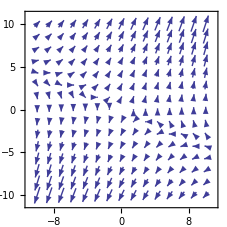

```mathematica
PlotMN[y,x+2y]
```

```mathematica
Curl[{y,x+2y,x},{x,y,z}]
```

{0,-1,0}

```mathematica
VectorPlot3D[{0,-1,0},{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
m[x_,y_]:=y
n[x_,y_]:=x+2y
```

```mathematica
findPotential[M_, N_]:=
Module[{c = Curl[{M,N},{x,y}],H= Integrate[M,x],g=D[H,y]},
If[ c===0,
Integrate[N-D[H,y],y]+H,"DNE"]
]
```

```mathematica
(*It works!*)
```

```mathematica
findPotential[y, x+2y]
```

x y+y^2

```mathematica
Plot3D[x*y+y^2,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
findPotential[x^3y^4,x^4y^3]
```

(x^4 y^4)/4

```mathematica
findPotential[x^2y,-x*y^2]
```

DNE

```mathematica
GraphicsRow[{},{}]
```